```mathematica
(* 01 *)
```

99.47

```mathematica
(* 02 *)
```

231. m

```mathematica
(* 03 *)
```

-5.5 °C

```mathematica
(* 04 *)
```

Failure[…]

```mathematica
(* 05 *)
ChemicalData["Benzene","BoilingPoint"]
```

80. °C

```mathematica
(* 06 *)
bp = Table[ChemicalData[c,"BoilingPoint"],{c,{"Benzene","Ethanol","Chloroform","Diethylamine","Pentane"}}];
Sort[bp]
```

{36.06 °C,55. °C,61. °C,78. °C,80. °C}

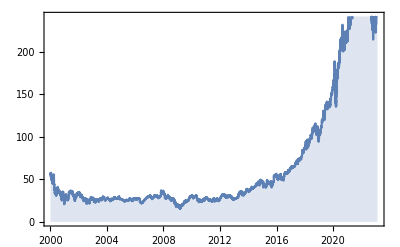

```mathematica
(* 07 *)
DateListPlot[FinancialData["MSFT",{2000,1,1}],Joined->True,Filling->Bottom]
```

```mathematica
(* 08 *)
Manipulate[DateListPlot[FinancialData[airline,{2000,1,1}],Joined->True,Filling->Bottom,PlotRange->{0,80}],{airline,{"LUV","DAL","UAL","AAL"}}]
```

```mathematica
(* 09 *)
Manipulate[CountryData[country,"Flag"],{country,CountryData["Asia"]}]
```

```mathematica
(* 10 *)
GenomeLookup["GGGTATAGGGTATAGAT"]
```

{{{Chromosome7,-1},{17796562,17796578}}}